```mathematica
Integrate[x^2+4,x]
```

4 x+x^3/3

```mathematica
Integrate[x^2+4,{x,1,3}]
```

50/3

```mathematica
Integrate[Sin[x]/Log[x],{x,2,5}]
```

∫_2^5 Sin[x]/Log[x]ⅆx

```mathematica
NIntegrate[Sin[x]/Log[x],{x,2,5}]
```

-0.20523

```mathematica
Integrate[x^2 y,{x,1,3},{y,0,5}]
```

325/3

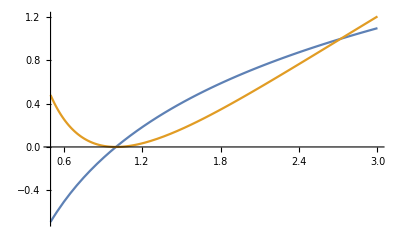

```mathematica
Plot[{Log[x],Log[x]^2},{x,0.5,3}]
```

```mathematica
(* First Method *)
Solve[Log[x]==Log[x]^2,x]
```

{{x→1},{x→ⅇ}}

```mathematica
Integrate[Log[x]-Log[x]^2,{x,1,ⅇ}]
```

3-ⅇ

```mathematica
(* Second Method *)
region=ImplicitRegion[{1≤x≤E,Log[x]^2≤y<=Log[x]},{x,y}]
```

ImplicitRegion[1≤x≤ⅇ&&Log[x]^2≤y≤Log[x],{x,y}]

```mathematica
RegionPlot[region]
```

-Graphics-

```mathematica
Integrate[1,{x,y}∈region]
```

3-ⅇ

```mathematica
(* Third Method *)
Integrate[1,{x,1,E},{y,Log[x]^2,Log[x]}]
```

3-ⅇ

```mathematica
(* Task1 // for Hubul *)
v[t_]:=0.001302 t^3-0.09029 t^2+23.61 t-3.083;
Minimize[{v'[t],0<=t≤126},t]
```

{21.5229,{t→23.1157}}

```mathematica
Maximize[{v'[t],0≤t≤126},t]
```

{62.8686,{t→126.}}

```mathematica
(* Task2 *)
Subscript[a, 0]=0.0518;
Subscript[a, 1]=2.0026;
Subscript[a, 2]=-4.491;
Subscript[d, 0]=7.82;
z1[x_,y_]:=Subscript[d, 0] √(1-(4 (x^2+y^2))/Subscript[d, 0]^2) (Subscript[a, 0]+(Subscript[a, 1] (x^2+y^2))/Subscript[d, 0]^2+(Subscript[a, 2] (x^2+y^2)^2)/Subscript[d, 0]^4);
z2[x_,y_]:=-Subscript[d, 0] √(1-(4 (x^2+y^2))/Subscript[d, 0]^2) (Subscript[a, 0]+(Subscript[a, 1] (x^2+y^2))/Subscript[d, 0]^2+(Subscript[a, 2] (x^2+y^2)^2)/Subscript[d, 0]^4);
Plot3D[{z1[x,y],z2[x,y]},{x,-5,5},{y,-5,5},PlotStyle->Red,Mesh->None]
```

-Graphics3D-

```mathematica
Clear[y]
```

```mathematica
Reduce[Subscript[d, 0] √(1-(4 (x^2+y^2))/Subscript[d, 0]^2) (Subscript[a, 0]+(Subscript[a, 1] (x^2+y^2))/Subscript[d, 0]^2+(Subscript[a, 2] (x^2+y^2)^2)/Subscript[d, 0]^4)==0,{x,y},,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-3.91≤x≤3.91&&(y==-0.01 √(152881.-10000. x^2)||y==0.01 √(152881.-10000. x^2))

```mathematica
NIntegrate[1,{x,-3.91,3.91},{y,-0.01 √(152881.-10000. x^2),0.01 √(152881.-10000. x^2)},{z,-Subscript[d, 0] √(1-(4 (x^2+y^2))/Subscript[d, 0]^2) (Subscript[a, 0]+(Subscript[a, 1] (x^2+y^2))/Subscript[d, 0]^2+(Subscript[a, 2] (x^2+y^2)^2)/Subscript[d, 0]^4),Subscript[d, 0] √(1-(4 (x^2+y^2))/Subscript[d, 0]^2) (Subscript[a, 0]+(Subscript[a, 1] (x^2+y^2))/Subscript[d, 0]^2+(Subscript[a, 2] (x^2+y^2)^2)/Subscript[d, 0]^4)}]
```

94.0984

```mathematica
(* 10.01 Task1 *)
N[Log[485]+√53]
```

13.4643

```mathematica
(* Task2 *)
Plot3D[x^2 Sin[y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
(* Task3 *)
taylorPoly[f_,n_,x0_]:=Sum[((D[f,{x,i}]/.x->x0)/i!)*(x-x0)^i,{i,0,n}];
Print[taylorPoly[x^3-3 x^2-3 ArcTan[x]+4,4,1.5]]
```

-2.32338-3.17308 (-1.5+x)+1.92604 (-1.5+x)^2+0.832499 (-1.5+x)^3+0.0504184 (-1.5+x)^4

```mathematica
(* Task 4 *)
NIntegrate[Cos[x]/(√(x^2+1)),{x,0,0.5}]
```

0.461999

```mathematica
Integrate[taylorPoly[Cos[x],7,0]/taylorPoly[√(x^2+1),7,0],{x,0,0.5}]
```

0.461994

```mathematica
(* Task 5 *)
Clear[a]
NSolve[a 2^4-(a+2) 2^3+3==7,a]
```

{{a→2.5}}

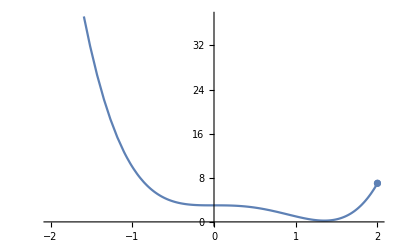

```mathematica
a=2.5;
Show[Plot[a x^4-(a+2) x^3+3,{x,-2,2}],ListPlot[{{2,7}}]]
```

```mathematica
(* Task 6 *)
Clear[n]
f[n_]:=(
For[k=2,k<=n,k++,
If[Det[Table[i-j^2,{i,k},{j,k}]]==0,Print["Yes"],Print["No"]]]
)
```

```mathematica
f[10]
```

No

Yes

Yes

Yes

«5 more identical outputs»

```mathematica
(* Task 7 *)
Clear[x,y,t,a,b,c,d,e]
x[t_]:=Cos[a t]-Cos[b t] Sin[c t];
y[t_]:=2 Sin[d t]-Sin[e t];
```

```mathematica
(* a *)
a=80;
b=1;
c=2;
d=1;
e=80;
g1=ParametricPlot[{x[t],y[t]},{t,-10,10},PlotLabels->"a=80, b=1, c=2, d=1, e=80"];
```

```mathematica
(* b *)
Clear[a,b,c,d,e]
a=1;
b=60;
c=1;
d=1;
e=60;
g2=ParametricPlot[{x[t],y[t]},{t,-10,10},PlotLabels->"a=1, b=60, c=1, d=1, e=60"];
```

```mathematica
GraphicsRow[{g1,g2}]
```

-Graphics-

```mathematica
(* Task 8 *)
Clear[list]
list=Table[RandomInteger[{1,100}],{i,1000}];
list1={};
For[i=1,i≤Length[list],i++,
If[EvenQ[list[[i]]],AppendTo[list1,list[[i]]]]]
```

```mathematica
(* Task 9 *)
Clear[f,g,x]
f[x_]:=Sin[x];
g[x_]:=(f[x+Δx]-f[x])/Δx;
Limit[g[x],Δx->0]
```

Cos[x]

```mathematica
D[f[x],x]
```

Cos[x]

```mathematica
Manipulate[Plot[{(f[x+Δx]-f[x])/Δx,Cos[x]},{x,-10,10},PlotRange->{-1,1}],{Δx,-5,0}]
```

```mathematica
(*Manipulate[GraphicsRow[{Plot[{f[x],(f[x+Δx]-f[x])/Δx},{x,-10,10},PlotRange->{-1,1}],Plot[Abs[f[x]-(f[x+Δx]-f[x])/Δx],{x,-10,10}]}],{Δx,-5,0}]*)
```

```mathematica
(* Task 10 *)
FindRoot[{y==ⅇ^(x-2),y^2==x},{x,1},{y,1}]
```

{x→0.019026,y→0.137935}

```mathematica
NSolve[{y==ⅇ^(x-2),y^2==x},{x,y},Reals]
```

{{x→0.019026,y→0.137935},{x→2.44754,y→1.56446}}

```mathematica
Plot3D[{y==e^(x-2),y^2==x},{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
(* Task 11 *)
Clear[f,x]
f[x_]:=Det[({{2, x, x^2, x^3}, {x, 0, x, x^2}, {x^2, x, 1, x}, {x^3, x^2, x, 4}})];
FindMinimum[{f[x],0≤x≤2016},x]
```

{-3.7037,{x→0.816497}}

```mathematica
FindMaximum[{f[x],0≤x≤2016},x]
```

{9.,{x→1.73205}}

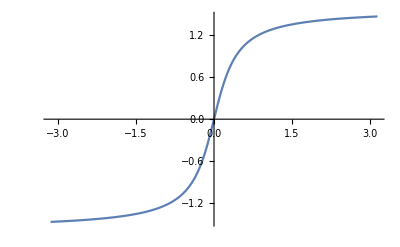

```mathematica
(* Task 12 *)
Clear[f,x]
f[x_]:=ArcTan[3 x];
(* a *)
Plot[f[x],{x,-π,π}]
```

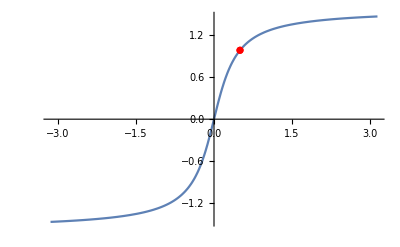

```mathematica
(* b *)
Show[{Plot[f[x],{x,-π,π}],ListPlot[{{0.5,f[0.5]}},PlotStyle->Red]}]
```

```mathematica
(* c *)
Clear[M]
M=Table[{Subscript[x, i],f[Subscript[x, i]]},{Subscript[x, i],-π,π,(2 π)/100.}]
```

{{-3.14159,-1.46509},{-3.07876,-1.46295},{-3.01593,-1.46072},{-2.9531,-1.4584},{-2.89027,-1.45597},{-2.82743,-1.45345},{-2.7646,-1.4508},{-2.70177,-1.44804},{-2.63894,-1.44515},{-2.57611,-1.44212},{-2.51327,-1.43894},{-2.45044,-1.4356},{-2.38761,-1.43208},{-2.32478,-1.42838},{-2.26195,-1.42448},{-2.19911,-1.42037},{-2.13628,-1.41601},{-2.07345,-1.4114},{-2.01062,-1.4065},{-1.94779,-1.4013},{-1.88496,-1.39577},{-1.82212,-1.38986},{-1.75929,-1.38355},{-1.69646,-1.37678},{-1.63363,-1.36951},{-1.5708,-1.36169},{-1.50796,-1.35325},{-1.44513,-1.3441},{-1.3823,-1.33417},{-1.31947,-1.32335},{-1.25664,-1.31151},{-1.19381,-1.29851},{-1.13097,-1.28418},{-1.06814,-1.2683},{-1.00531,-1.25063},{-0.942478,-1.23085},{-0.879646,-1.20858},{-0.816814,-1.18334},{-0.753982,-1.15453},{-0.69115,-1.12142},{-0.628319,-1.08303},{-0.565487,-1.03816},{-0.502655,-0.985235},{-0.439823,-0.922271},{-0.376991,-0.846783},{-0.314159,-0.755794},{-0.251327,-0.646045},{-0.188496,-0.514655},{-0.125664,-0.360515},{-0.0628319,-0.18631},{4.44089×10^-16,1.33227×10^-15},{0.0628319,0.18631},{0.125664,0.360515},{0.188496,0.514655},{0.251327,0.646045},{0.314159,0.755794},{0.376991,0.846783},{0.439823,0.922271},{0.502655,0.985235},{0.565487,1.03816},{0.628319,1.08303},{0.69115,1.12142},{0.753982,1.15453},{0.816814,1.18334},{0.879646,1.20858},{0.942478,1.23085},{1.00531,1.25063},{1.06814,1.2683},{1.13097,1.28418},{1.19381,1.29851},{1.25664,1.31151},{1.31947,1.32335},{1.3823,1.33417},{1.44513,1.3441},{1.50796,1.35325},{1.5708,1.36169},{1.63363,1.36951},{1.69646,1.37678},{1.75929,1.38355},{1.82212,1.38986},{1.88496,1.39577},{1.94779,1.4013},{2.01062,1.4065},{2.07345,1.4114},{2.13628,1.41601},{2.19911,1.42037},{2.26195,1.42448},{2.32478,1.42838},{2.38761,1.43208},{2.45044,1.4356},{2.51327,1.43894},{2.57611,1.44212},{2.63894,1.44515},{2.70177,1.44804},{2.7646,1.4508},{2.82743,1.45345},{2.89027,1.45597},{2.9531,1.4584},{3.01593,1.46072},{3.07876,1.46295},{3.14159,1.46509}}

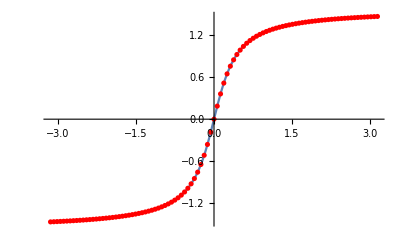

```mathematica
(* d *)
Show[{Plot[f[x],{x,-π,π}],ListPlot[{M},PlotStyle->Red]}]
```

```mathematica
(* Task 13 *)
Clear[f]
f[x_]:=Piecewise[{{1-Sin[8 x], x<0}, {1-x^2, 0≤x≤1}, {x^3-1, 1≤x}}];
```

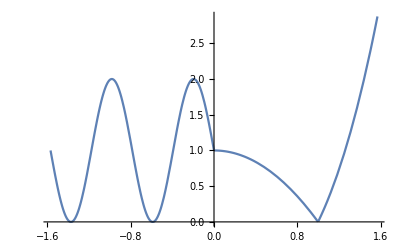

```mathematica
Plot[f[x],{x,-π/2,π/2}]
```

```mathematica
Minimize[f[x],x]
```

{0,{x→1}}

```mathematica
NMaximize[{f[x],-π/2≤x≤π/2},x]
```

{2.87578,{x→1.5708}}

```mathematica
(* Task 14 *)
Clear[f,x,k,M]
k=4 x^3-3 √x;
M={1,0};
```

```mathematica
Integrate[k,x]
```

-2 x^(3/2)+x^4

```mathematica
Solve[y==x^4-2 x^(3/2)+c/.{x->1,y->0},c]
```

{{c→1}}

```mathematica
f[x_]:=x^4-2 x^(3/2)+1;
Solve[0==f'[1] 1+b,b]
```

{{b→-1}}

```mathematica
f'[1]
```

1

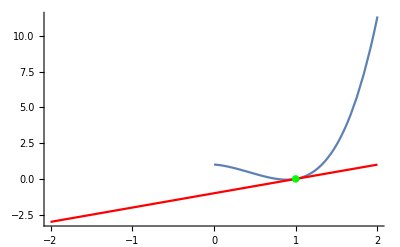

```mathematica
Show[{Plot[f[x],{x,-2,2},PlotRange->All],Plot[x-1,{x,-2,2},PlotStyle->Red],ListPlot[{{M}},PlotStyle->Green]}]
```

```mathematica
(* Task 15 *)
Clear[t,A,x,a]
f[t_]:=Det[Table[∫_(π/4)^t (Cos[x]+Sin[x])/(i+j)ⅆx,{i,3},{j,3}]];
Series[f[t],{t,0,10}]
```

-1/43200+t/14400-t^2/28800-t^3/17280+(13 t^4)/345600+(41 t^5)/1728000-(121 t^6)/10368000-(73 t^7)/14515200+(1093 t^8)/580608000+(3281 t^9)/5225472000-(9841 t^10)/52254720000+O[t]^11

```mathematica
(* Task 16 *)
Clear[f,x,x0,Δx,M,a,b]
f[x_]:=-x^4+2 x;
x0=1;
M={x0,f[x0]};
```

```mathematica
f'[x]
```

2-4 x^3

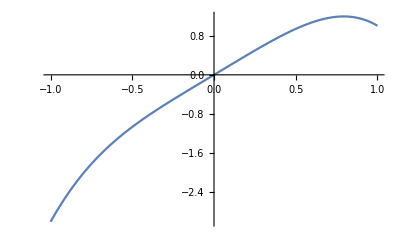

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
f[x0]
```

1

```mathematica
f'[x0]
```

-2

```mathematica
Solve[f[f[x0]]==f'[x0] x0+b,b]
```

{{b→3}}

```mathematica
Solve[{a x0+b==f[x0],a (x0+Δx)+b==f[x0+Δx]},{a,b}]
```

{{a→-2-6 Δx-4 Δx^2-Δx^3,b→3+6 Δx+4 Δx^2+Δx^3}}

```mathematica
Manipulate[Show[Plot[f[x],{x,-3.5,3.5},PlotRange->Full,PlotLabels->"f[x]"],Plot[x+3,{x,
-3.5,3.5},PlotLabels->"f'[x]"],Plot[(-2-6 Δx-4 Δx^2-Δx^3) x+(3+6 Δx+4 Δx^2+Δx),{x,-3.5,3.5},PlotLabels->"sec"]],{Δx,1,0}]
```